## Simple Reservoir Model

Integrated Model - PP590
Tiago Amorim, RA: 100.675

Actual calculations start in Part 5 .

Latest version in: https://github.com/TiagoCAAmorim/IntegratedModel/tree/main/docs/Report2_reservoir

```mathematica
ClearAll;
```

## Proposed Problem

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Resolution

### Part 1 - Formulation

Assuming black-oil formulation and that there is no free gas in the reservoir, we can simplify this problem to two equations:

-Graphics-   and   -Graphics-

Applying finite differences, using the implicit form for a 1D problem and multiplying by the block volume (V):

∑_(i={i,j,k}) [T_(p,i+1/2)(Φ_(p,i+1)-Φ_(p,i))+T_(p,i-1/2)(Φ_(p,i-1)-Φ_(p,i))]^(n+1)=V_i/Δt[((ϕS_p/B_p)_i)^(n+1)-((ϕS_p/B_p)_i)^n]+(q_(p,i))^well

Where:
   p is either oil or water
   q^well is in standard conditions 
   i is one of the main flow directions (i,j,k)

The transmissibility in the x-direction is calculated between blocks (equivalent expressions for the other directions):

T_(p,i+1/2)=(λ_p(Δx Δy Δz)/Δx^2)_(i+1/2)=(k kr_p/(B_p μ_p)(Δx Δy Δz)/Δx^2)_(i+1/2)=((k A)/Δx)_(i+1/2)(1/(B_p μ_p))_(i+1/2)kr_(p,i+1/2)
((k_i A)/Δx)_(i+1/2)=(A_(i+1/2))/((x_(i+1)-x_(i+1/2))/(k_(i,i+1))+(x_(i+1/2)-x_i)/(k_(i,i)))

The first part is related to the reservoir characteristics:

((k_i A)/Δx)_(i+1/2)=(A_(i+1/2))/((x_(i+1)-x_(i+1/2))/(k_(i,i+1))+(x_(i+1/2)-x_i)/(k_(i,i)))

Where:
   x_(i+1/2)-x_i is the distance in i direction between the cell center of cells i and the interface between cells i + i+1
   A_(i+1/2) is the flow area in common between cells i and i+1

The second part is a function of pressure:

(1/(B_p μ_p))_(i+1/2)=((1/(B_p μ_p))_i+(1/(B_p μ_p))_(i+1))/2

The third part is a function of saturation and equal to the value in the upstream block (larger pressure):

kr_(p,i+1/2)=kr_(p,"upstream")

Given that for the proposed problem:
   Φ_(p,i)= P_(p,i) (no vertical displacement)
   P_o = P_w=P (no capillary pressure)
   S_o=1-S_w (no free gas)
   B_o,B_w, μ_o,μ_w, k, Δx, Δy, Δz, V are constants
   1-D problem, in the x direction
   Flow is from the injector (i=1) to the producer (i=3)
The transmissibility becomes:

T_(p,i+1/2)=(k Δy Δz)/Δx 1/(B_p μ_p)kr_(p,i)

The formulation reduces to:

[T_(p,i+1/2)(P_(i+1)-P_i)+T_(p,i-1/2)(P_(i-1)-P_i)]^(n+1)=ΔxΔyΔz/Δt ϕ/B_p[(S_(p,i))^(n+1)-(S_(p,i))^n]+(q_(p,i))^well

(k Δy Δz)/Δx(1/(B_p μ_p)[kr_(p,i)(P_(i+1)-P_i)+kr_(p,i-1)(P_(i-1)-P_i)])^(n+1)=ΔxΔyΔz/Δt ϕ/B_p[(S_(p,i))^(n+1)-(S_(p,i))^n]+(q_(p,i))^well

Which can be write in as a f(x)=0 problem:

(k Δy Δz)/Δx(1/(B_p μ_p)[kr_(p,i)P_(i+1)])^(n+1)-(k Δy Δz)/Δx(1/(B_p μ_p)[(kr_(p,i)+kr_(p,i-1))P_i])^(n+1)+(k Δy Δz)/Δx(1/(B_p μ_p)[kr_(p,i-1)P_(i-1)])^(n+1)
-ΔxΔyΔz/Δt ϕ/B_p(S_(p,i))^(n+1)+ΔxΔyΔz/Δt ϕ/B_p(S_(p,i))^n-(q_(p,i))^well=0

Where:
   (S_(p,i))^0 is known
   P_i^0 is known

Problem variables:
   (S_(p,i))^n and P_i^n, with n={1,2,...,n_(t end)}
Important to remember that:
   kr_p=f(S_p)

### Part 2 - Wells

For cell i=1 there is an injector with constant water injection rate:

(q_(w,1))^well=Q_w
(q_(o,1))^well=0

Cell i=2 has no wells:

(q_(w,2))^well=0
(q_(o,2))^well=0

Cell i=3 has a producer with constant bottom-hole pressure (p_wf):

(q_(w,3))^well=WI kr_w/(B_w μ_w)(P_wf-P_3)
(q_(o,3))^well=WI kr_o/(B_o μ_o)(P_wf-P_3)

With Δx=Δy and k_x=k_y=k:

WI=(2π k Δz)/(ln(r_e/r_w)+S)=(2π k Δz)/(ln((0.208Δx)/r_w))

### Part 3 - System of equations

Some additional constants to simplify the notation:

(k Δy Δz)/Δx 1/(B_p μ_p)=α_p

ΔxΔyΔz ϕ/B_p=β_p

WI 1/(B_p μ_p)=τ_p

Thus, the main formula becomes:

α_p[kr_(p,i)P_(i+1)]^(n+1)-α_p[(kr_(p,i)+kr_(p,i-1))P_i]^(n+1)+α_p[kr_(p,i-1)P_(i-1)]^(n+1)-β_p(S_(p,i))^(n+1)+β_p(S_(p,i))^n-(q_(p,i))^well=0

Plugging everything together:

α_o[kr_(o,1)P_2]^(n+1)-α_o[kr_(o,1)P_1]^(n+1)+β_o/Δt(S_(w,1))^(n+1)-β_o/Δt(S_(w,1))^n=0
α_w[kr_(w,1)P_2]^(n+1)-α_w[kr_(w,1)P_1]^(n+1)-β_w/Δt(S_(w,1))^(n+1)+β_w/Δt(S_(w,1))^n-Q_w=0

α_o[kr_(o,2)P_3]^(n+1)-α_o[(kr_(o,2)+kr_(o,1))P_2]^(n+1)+α_o[kr_(o,1)P_1]^(n+1)+β_o/Δt(S_(w,2))^(n+1)-β_o/Δt(S_(w,2))^n=0
α_w[kr_(w,2)P_3]^(n+1)-α_w[(kr_(w,2)+kr_(w,1))P_2]^(n+1)+α_w[kr_(w,1)P_1]^(n+1)-β_w/Δt(S_(w,2))^(n+1)+β_w/Δt(S_(w,2))^n=0

-α_o[kr_(o,2)P_3]^(n+1)+α_o[kr_(o,2)P_2]^(n+1)+β_o/Δt(S_(w,3))^(n+1)-β_o/Δt(S_(w,3))^n+τ_o[kr_(o,3)]^(n+1)P_wf-τ_o[kr_(o,3)P_3]^(n+1)=0
-α_w[kr_(w,2)P_3]^(n+1)+α_w[kr_(w,2)P_2]^(n+1)-β_w/Δt(S_(w,3))^(n+1)+β_w/Δt(S_(w,3))^n+τ_w[kr_(w,3)]^(n+1)P_wf-τ_w[kr_(w,3)P_3]^(n+1)=0

### Part 4 - Newton-Raphson

Since it is not possible to directly solve the system of equations, Newton-Raphson will be employed to search for the answer in each time-step.
Rewriting the problem in matrix form (K x = f):

(-α_o[kr_(o,1)]^(n+1) | β_o/Δt | α_o[kr_(o,1)]^(n+1) |  0 | 0  | 0 
-α_w[kr_(w,1)]^(n+1) | -β_w/Δt | α_w[kr_(w,1)]^(n+1) |  0 | 0  | 0 
α_o[kr_(o,1)]^(n+1) | 0 | -α_o[kr_(o,2)+kr_(o,1)]^(n+1) | β_o/Δt | α_o[kr_(o,2)]^(n+1) | 0 
α_w[kr_(w,1)]^(n+1) | 0 | -α_w[kr_(w,2)+kr_(w,1)]^(n+1) | -β_w/Δt | α_w[kr_(w,2)]^(n+1) | 0
0 | 0 | α_o[kr_(o,2)]^(n+1) | 0 | -α_o[kr_(o,2)]^(n+1)-τ_o[kr_(o,3)]^(n+1) | β_o/Δt
0 | 0 | α_w[kr_(w,2)]^(n+1) | 0 | -α_w[kr_(w,2)]^(n+1)-τ_w[kr_(w,3)]^(n+1) | -β_w/Δt)(P_1^(n+1)
(S_(w,1))^(n+1)
P_2^(n+1)
(S_(w,2))^(n+1)
P_3^(n+1)
(S_(w,3))^(n+1))=(β_o/Δt(S_(w,1))^n
-β_w/Δt(S_(w,1))^n+Q_w
β_o/Δt(S_(w,2))^n
-β_w/Δt(S_(w,2))^n
β_o/Δt(S_(w,3))^n-τ_o[kr_(o,3)]^(n+1)P_wf
-β_w/Δt(S_(w,3))^n-τ_w[kr_(w,3)]^(n+1)P_wf)

To use Newton-Raphson it is needed the Jacobian of R = (K x - f):

J=K+(0 | α_o (P_2^(n+1)-P_1^(n+1))(∂kr_(o,1))/(∂S_(w,1)) | 0 |  0 | 0  | 0 
0 | α_w (P_2^(n+1)-P_1^(n+1))(∂kr_(w,1))/(∂S_(w,1)) | 0 |  0 | 0  | 0 
0 | -α_o (P_2^(n+1)-P_1^(n+1))(∂kr_(o,1))/(∂S_(w,1)) | 0 | α_o (P_3^(n+1)-P_2^(n+1))(∂kr_(o,2))/(∂S_(w,2)) | 0 | 0 
0 | -α_w (P_2^(n+1)-P_1^(n+1))(∂kr_(w,1))/(∂S_(w,1)) | 0 | α_w (P_3^(n+1)-P_2^(n+1))(∂kr_(w,2))/(∂S_(w,2)) | 0 | 0
0 | 0 | 0 | -α_o (P_3^(n+1)-P_2^(n+1))(∂kr_(o,2))/(∂S_(w,2)) | 0 | -τ_o[P_3-P_wf]^(n+1)(∂kr_(o,3))/(∂S_(w,3))
0 | 0 | 0 | -α_w (P_3^(n+1)-P_2^(n+1))(∂kr_(w,2))/(∂S_(w,2)) | 0 | -τ_w[P_3-P_wf]^(n+1)(∂kr_(w,3))/(∂S_(w,3)))

Newton-Raphson algorithm (with simplified convergence controls):

Define initial Δt
   Start with the initial state (x^0)
   For i=1,...,n
      Make x_0^i=x^(i-1)
      Repeat
         Calculate f, K and J
         x_(j+1)^i=x_j^i-J^-1(Kx-f)
      Until convergence: ||K x - f|| < ϵ or j=j_max
      if Δ_t P>Δ_t P_max or Δ_t S>Δ_t S_max then
         Δt^new=Δt/2
         Repeat time-step (j--)
      else
         Δt^new=1.2 Δt
         x^i=x_(j+1)^i

### Part 5 - Relative Permeability

Actual calculations start in the next cells.

The provided plot was manually digitalized, and the curves were approximated with known Kr correlations. The major endpoints are:

```mathematica
Swc=0.10;
Swcr=0.20;
Sor=0.16;
Krwmax = 0.63;
Kromax=1.00;
```

The water curve was adjusted to the Corey formulation:

```mathematica
nw=2;
Swd=(Sw-Swcr)/(1-Swcr-Sor);
krw=Piecewise[{
{0,Sw<Swc},
{0,Sw<Swcr},
{Krwmax*Power[Swd,nw],Sw<=1-Sor},
{Krwmax+(1-Krwmax)*(Sw-1+Sor)/Sor,Sw<=1},
{1,Sw>1}
}];
dkrw=D[krw,Sw];
```

The oil curve was adjusted to the LET formulation :

```mathematica
Lo=1.7;
Eo=1.;
To=2.;
Sod=1-(Sw-Swc)/(1-Swc-Sor);
krow=Piecewise[{
{Kromax,Sw<Swc},
{Kromax*Power[Sod,Lo]/(Power[Sod,Lo]+Eo*Power[1-Sod,To]),Sw<=1-Sor},
{0,Sw<1},
{0,Sw>1}
}];
dkrow=D[krow,Sw];
```

```mathematica
Plot[{krw,krow,krw+krow,krw/(krow+krw)},{Sw,0,1},
AxesLabel->{"Sw","Kr"},
PlotLabel->"Relative Permeability",
PlotLabels->"Expressions",
GridLines->Automatic,
PlotRange->{{0,1},{0,1}}]
Plot[{D[krw,Sw]/.Sw->s, D[krow,Sw]/.Sw->s},{s,0,1},
AxesLabel->{"Sw","dKr/dSw"},
PlotLabel->"Relative Permeability Derivatives",
PlotLabels->"Expressions",
GridLines->Automatic,
PlotRange->Full]
```

-Graphics-

-Graphics-

Since Swi is defined as 0.20 in the proposed problem, it will be modified in the relative permeability parameters as well.

```mathematica
Swc=0.20;
Swcr=0.20;
Sor=0.16;
Krwmax = 0.63;
Kromax=1.00;
nw=2;
Swd=(Sw-Swcr)/(1-Swcr-Sor);
krw=Piecewise[{
{0,Sw<Swc},
{0,Sw<Swcr},
{Krwmax*Power[Swd,nw],Sw<=1-Sor},
{Krwmax+(1-Krwmax)*(Sw-1+Sor)/Sor,Sw<=1},
{1,Sw>1}
}];
Lo=1.7;
Eo=1.;
To=2.;
Sod=1-(Sw-Swc)/(1-Swc-Sor);
krow=Piecewise[{
{Kromax,Sw<Swc},
{Kromax*Power[Sod,Lo]/(Power[Sod,Lo]+Eo*Power[1-Sod,To]),Sw<=1-Sor},
{0,Sw<1},
{0,Sw>1}
}];
dkrw=D[krw,Sw];
dkrow=D[krow,Sw];
```

### Part 6 - Numerical Example

-Graphics-

-Graphics-

#### Problem description

```mathematica
Pinit=340.; (* bar *)
Swi=0.2;
k=1000; (* mD *)
ϕ=0.3;
Δx=Δy=200.; (* m *)
Δz=30.; (* m *)
Bo=1.01;
μo=130.; (* cP *)
Bw=1.;
μw=1.; (* cP *)
rw=4.*2.54/100; (* m *)
S=0.;
Qwi=-350.; (* m3/d *)
Pwf=330.; (* bar *)
tEnd=5*365.; (* days*)
```

#### Constants (with proper unit conversion)

```mathematica
αo=((k 9.869233 10^-16) Δy Δz)/Δx 1/(Bo (μo 10^-3))10^5(24 60 60);
αw=((k 9.869233 10^-16) Δy Δz)/Δx 1/(Bw (μw 10^-3))10^5(24 60 60);
```

```mathematica
βo=Δx Δy Δz ϕ/Bo;
βw=Δx Δy Δz ϕ/Bw;
```

```mathematica
WI=(2π (k 9.869233 10^-16) Δz)/(Log[(0.208Δx)/rw]+S);
```

```mathematica
τo=WI 1/(Bo (μo 10^-3))10^5(24 60 60);
τw=WI 1/(Bw (μw 10^-3))10^5(24 60 60);
```

#### Some Quantities

```mathematica
Print["Pore volume: ",Δx Δy Δz ϕ," m3"]
```

Pore volume: 360000. m3

```mathematica
Print["Time do inject 1% of pore volume: ",-0.01*Δx Δy Δz ϕ/Qwi," days"]
```

Time do inject 1% of pore volume: 10.2857 days

```mathematica
Print["Initial potential producer flow rate: ",τo(Pinit-Pwf) krow/.Sw->Swi," m3/d"]
```

Initial potential producer flow rate: 20.3522 m3/d

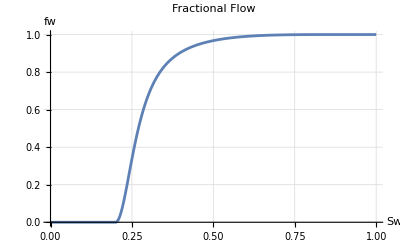

```mathematica
fw=Piecewise[{
{0,Sw<=Swi},
{1/(1+(krow/(Bo μo))/(krw/(Bw μw))),True}
}];
Plot[{fw/.Sw->s},{s,0,1},
AxesLabel->{"Sw","fw"},
PlotLabel->"Fractional Flow",
GridLines->Automatic,
PlotRange->Full]
```

#### Main functions

```mathematica
buildK[x_,Δt_]:=Block[{Sw,kro1,kro2,kro3,krw1,krw2,krw3,K},
kro1 = krow/.Sw->x[[2]];
krw1 = krw/.Sw->x[[2]];
kro2 = krow/.Sw->x[[4]];
krw2 = krw/.Sw->x[[4]];
kro3 = krow/.Sw->x[[6]];
krw3 = krw/.Sw->x[[6]];
K={{-αo kro1,βo/Δt,αo kro1,0,0,0}};
K=ArrayFlatten[{{K},{{{-αw krw1,-βw/Δt,αw krw1,0,0,0}}}}];
K=ArrayFlatten[{{K},{{{αo kro1,0,-αo(kro2+kro1),βo/Δt,αo kro2,0}}}}];
K=ArrayFlatten[{{K},{{{αw krw1,0,-αw(krw2+krw1),-βw/Δt,αw krw2,0}}}}];
K=ArrayFlatten[{{K},{{{0,0,αo kro2,0,-αo kro2-τo kro3,βo/Δt}}}}];
K=ArrayFlatten[{{K},{{{0,0,αw krw2,0,-αw krw2-τw krw3,-βw/Δt}}}}];
K]
```

```mathematica
buildF[xNew_,xOld_,Δt_]:=Block[{Sw,F,kro3,krw3},
kro3 = krow/.Sw->xNew[[6]];
krw3 = krw/.Sw->xNew[[6]];
F={0,0,0,0,0,0};
F[[1]] = βo/Δt xOld[[2]];
F[[2]] = -βw/Δt xOld[[2]]+Qwi;
F[[3]] = βo/Δt xOld[[4]];
F[[4]] = -βw/Δt xOld[[4]];
F[[5]] = βo/Δt xOld[[6]]-τo kro3 Pwf;
F[[6]] = -βw/Δt xOld[[6]]-τw krw3 Pwf;
F]
```

```mathematica
buildJ[x_,Δt_]:=Block[{Sw,dkro1,dkro2,dkro3,dkrw1,dkrw2,dkrw3,J},
dkro1 = dkrow/.Sw->x[[2]];
dkrw1 = dkrw/.Sw->x[[2]];
dkro2 = dkrow/.Sw->x[[4]];
dkrw2 = dkrw/.Sw->x[[4]];
dkro3 = dkrow/.Sw->x[[6]];
dkrw3 = dkrw/.Sw->x[[6]];
J=buildK[x,Δt];

J[[1]][[2]] += αo (x[[3]]-x[[1]])dkro1;
J[[2]][[2]] += αw (x[[3]]-x[[1]])dkrw1;

J[[3]][[2]] += -αo (x[[3]]-x[[1]])dkro1;
J[[4]][[2]] += -αw (x[[3]]-x[[1]])dkrw1;
J[[3]][[4]] += αo (x[[5]]-x[[3]])dkro2;
J[[4]][[4]] += αw (x[[5]]-x[[3]])dkrw2;

J[[5]][[4]] += -αo (x[[5]]-x[[3]])dkro2;
J[[6]][[4]] += -αw (x[[5]]-x[[3]])dkrw2;
J[[5]][[6]] += -τo (x[[5]]-Pwf)dkro3;
J[[6]][[6]] += -τw (x[[5]]-Pwf)dkrw3;
J]
```

```mathematica
buildR[x_,xOld_,Δt_,verbose_]:=Block[{K,F,R},
K = buildK[x,Δt];
F = buildF[x,xOld,Δt];
R=Dot[K,x] - F;
If[verbose,
Print["X=",MatrixForm[x]];
Print["K=",MatrixForm[K]];
Print["F=",MatrixForm[F]];
Print["R=",MatrixForm[R]];
];
R]
```

```mathematica
solveNextX[xOld_,Δt_,verbose_]:=Block[{K,F,J,R,x, dx,MaxDeltaP,MaxDeltaS},
x = xOld;
n=1;
If[False,Print["Initial value"]];
R = buildR[x,xOld,Δt,False];
While[n<=10 &&Norm[R]>10^-6,
J = buildJ[x,Δt];
dx=LinearSolve[J,-R];
x+=dx;
If[False,Print["Iteration ",n]];
R = buildR[x,xOld,Δt,False];
n++];
dx=x-xOld;
MaxDeltaP=Max[Abs[dx[[1]]],Abs[dx[[3]]],Abs[dx[[5]]]];
MaxDeltaS=Max[Abs[dx[[2]]],Abs[dx[[4]]],Abs[dx[[6]]]];
If[verbose,Print["   iterations: ",n,"; ||R||=",Norm[R]," MaxΔP=",MaxDeltaP ," MaxΔS=",MaxDeltaS ]];
{x,dx}
]
```

```mathematica
checkConvergence[ΔPmax_,ΔSmax_,dx_]:=Block[{MaxDeltaP,MaxDeltaS,ok},
MaxDeltaP=Max[Abs[dx[[1]]],Abs[dx[[3]]],Abs[dx[[5]]]];
MaxDeltaS=Max[Abs[dx[[2]]],Abs[dx[[4]]],Abs[dx[[6]]]];
ok = (MaxDeltaP <ΔPmax) && (MaxDeltaS <ΔSmax);
ok
]
```

```mathematica
runSim[xInit_,ΔPmax_,ΔSmax_,Δtmax_,ΔtInit_,verbose_]:=Block[{x,Δt,t,xLast,xNew,dx, dxNew,i},
Δt=ΔtInit;
t={0};
x={xInit};
dx={{0,0,0,0,0,0}};
xLast = xInit;
For[i=0,t[[i+1]]<tEnd,i++,
If[verbose,Print["Time-step: ",i+1,",  Time: ",t[[i+1]]+Δt,",  Δt: ",Δt," days"]];
{xNew,dxNew}=solveNextX[xLast,Δt,verbose];
(* In this incompressible system the first dP is very high, an so it will be ignored in the 1st time-step. *)
If[checkConvergence[If[Length[t]>1,ΔPmax,10^6],ΔSmax,dxNew],
xLast=xNew;
AppendTo[t,t[[i+1]]+Δt];
AppendTo[x,xNew];
AppendTo[dx,dxNew];
Δt=Min[1.2 Δt,Δtmax,tEnd-t[[i+2]]];
,
Δt=0.5 Δt;
If[verbose,Print["Convergence criteria failed. New Δt: ",Δt," days"]];
i--;
];
];
{t,x,dx}
]
```

```mathematica
postProcess[t_,x_,dx_]:=Block[{i,n,P1,P2,P3,S1,S2,S3,t2,dP1,dP2,dP3,dS1,dS2,dS3,kro3,krw3,Qop,Qwp,Qlp,Qwiv,Wcut},

Print[ListLinePlot[{Transpose[{t,Join[{0},Differences[t]]}]},
AxesLabel->{"Time [days]","Δt [days]"},
PlotLabel->"Time-Step Size",
GridLines->Automatic,
PlotRange->Full]];

n=Length[t];
P1=Table[x[[i]][[1]],{i, n}];
P2=Table[x[[i]][[3]],{i,n}];
P3=Table[x[[i]][[5]],{i,n}];
S1=Table[x[[i]][[2]],{i,n}];
S2=Table[x[[i]][[4]],{i,n}];
S3=Table[x[[i]][[6]],{i,n}];

Print[ListLinePlot[{Transpose[{t,P1}],Transpose[{t,P2}],Transpose[{t,P3}]},
AxesLabel->{"Time [days]","Pressure [bar]"},
PlotLabel->"Block Pressures",
PlotLabels->{"P1","P2","P3"},
GridLines->Automatic,
PlotRange->Full]];

Print[ListLinePlot[{Transpose[{t,S1*100}],Transpose[{t,S2*100}],Transpose[{t,S3*100}]},
AxesLabel->{"Time [days]","Saturation [%]"},
PlotLabel->"Block Saturarions",
PlotLabels->{"S1","S2","S3"},
GridLines->Automatic,
PlotRange->Full]];

(* In this incompressible system the first dP is very high, an so it will be ignored in the 1st time-step. *)
t2=Take[t,-(n-2)];
dP1=Table[dx[[i+2]][[1]],{i, n-2}];
dP2=Table[dx[[i+2]][[3]],{i,n-2}];
dP3=Table[dx[[i+2]][[5]],{i,n-2}];
dS1=Table[dx[[i+2]][[2]],{i,n-2}];
dS2=Table[dx[[i+2]][[4]],{i,n-2}];
dS3=Table[dx[[i+2]][[6]],{i,n-2}];

Print[ListLinePlot[{Transpose[{t2,dP1}],Transpose[{t2,dP2}],Transpose[{t2,dP3}]},
AxesLabel->{"Time [days]","ΔPressure [bar]"},
PlotLabel->"Block Delta Pressures",
PlotLabels->{"ΔP1","ΔP2","ΔP3"},
GridLines->Automatic,
PlotRange->Full]];

Print[ListLinePlot[{Transpose[{t2,dS1*100}],Transpose[{t2,dS2*100}],Transpose[{t2,dS3*100}]},
AxesLabel->{"Time [days]","ΔSaturation [%]"},
PlotLabel->"Block Delta Saturarions",
PlotLabels->{"ΔS1","ΔS2","ΔS3"},
GridLines->Automatic,
PlotRange->Full]];

kro3 = Table[krow/.Sw->S3[[i]],{i,n}];
krw3 = Table[krw/.Sw->S3[[i]],{i, n}];
Qop=Table[τo kro3[[i]] (P3[[i]]-Pwf),{i, n}];
Qwp=Table[τw krw3[[i]] (P3[[i]]-Pwf),{i, n}];
Qlp=Qop+Qwp;
Qwiv=Table[-Qwi,{i, n}];
Wcut=Qwp/(Qop+Qwp);

colors={Green,Blue,Black,Purple};
Print[ListLinePlot[{Transpose[{t,Qop}],Transpose[{t,Qwp}],Transpose[{t,Qlp}],Transpose[{t,Qwiv}]},
AxesLabel->{"Time [days]","Liquid Flow [m3/d]"},
PlotLabel->"Well Rates",
PlotLabels->{"Qop","Qwp","Qlp","Qwi"},
PlotStyle->colors,
GridLines->Automatic,
PlotRange->Full]];

Print[ListLinePlot[{Transpose[{t,Wcut*100}]},
AxesLabel->{"Time [days]","Water-cut [%]"},
PlotLabel->"Water Cut",
GridLines->Automatic,
PlotRange->Full]];
]
```

#### Simulation

```mathematica
xInit={Pinit,Swi,Pinit,Swi,Pinit,Swi};
```

```mathematica
{t,x,dx}=runSim[xInit,1,0.005, 10,1,False];
```

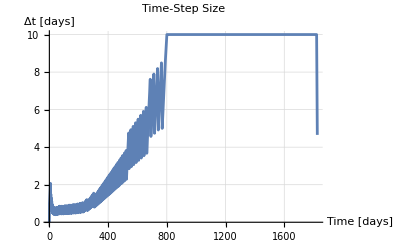

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

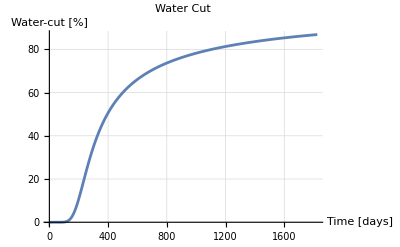

```mathematica
postProcess[t,x,dx]
```